```mathematica
n=1000;
(*X=Table[RandomReal[{0,10}],{i,1,n}];*)
X=RandomVariate[NormalDistribution[5,3],n];
δW=0.001;
δY=0.5;
dW=RandomVariate[NormalDistribution[0,√δW],n];
dY=RandomVariate[NormalDistribution[0,√δY],n];
W=Table[X[[i]]+dW[[i]],{i,1,n}];
Y=Table[5+2 X[[i]]+dY[[i]],{i,1,n}];
dataWY=Table[{W[[i]],Y[[i]]},{i,1,n}];
dataYW=Table[{Y[[i]],W[[i]]},{i,1,n}];
```

```mathematica
LinearModelFit[dataWY,x,x]["ParameterTable"]
LinearModelFit[dataWY,x,x]["ParameterConfidenceIntervalTable"]
LinearModelFit[dataWY,x,x]["ANOVATable"]
LinearModelFit[dataWY,x,x]["RSquared"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 5.03214 | 0.044216 | 113.808 | 6.88023320676×10^-574
x | 1.99824 | 0.00765205 | 261.139 | 6.10424440134×10^-921

| Estimate | Standard Error | Confidence Interval
1 | 5.03214 | 0.044216 | {4.94537,5.11891}
x | 1.99824 | 0.00765205 | {1.98323,2.01326}

| DF | SS | MS | F-Statistic | P-Value
x | 1 | 34961.7 | 34961.7 | 68193.4 | 6.10424440134×10^-921
Error | 998 | 511.66 | 0.512685 |  | 
Total | 999 | 35473.4 |  |  |

0.985576

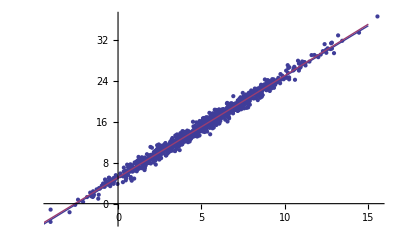

```mathematica
Show[
ListPlot[dataWY],
Plot[Evaluate[LinearModelFit[dataWY,x,x]["MeanPredictionBands"]],{x,-5,15}]
]
```

```mathematica
LinearModelFit[dataYW,x,x]["ParameterTable"]
LinearModelFit[dataYW,x,x]["ParameterConfidenceIntervalTable"]
LinearModelFit[dataYW,x,x]["ANOVATable"]
fitYW=LinearModelFit[dataYW,x,x]["ParameterTableEntries"];
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -2.41037 | 0.0303945 | -79.3028 | 3.89646811238×10^-433
x | 0.493221 | 0.00188873 | 261.139 | 6.10424440133×10^-921

| Estimate | Standard Error | Confidence Interval
1 | -2.41037 | 0.0303945 | {-2.47001,-2.35072}
x | 0.493221 | 0.00188873 | {0.489515,0.496927}

| DF | SS | MS | F-Statistic | P-Value
x | 1 | 8629.5 | 8629.5 | 68193.4 | 6.10424440134×10^-921
Error | 998 | 126.291 | 0.126545 |  | 
Total | 999 | 8755.79 |  |  |

```mathematica
{-fitYW[[1,1]]/fitYW[[2,1]],√((fitYW[[1,2]]/fitYW[[2,1]])^2+((fitYW[[1,1]]fitYW[[2,2]])/fitYW[[2,1]]^2)^2)}
{1/fitYW[[2,1]],fitYW[[2,2]]/fitYW[[2,1]]^2}
```

{4.887,0.0644035}

{2.02749,0.00776403}

```mathematica
wbar=Mean[W]
ybar=Mean[Y]
Sww=Variance[W]
Swy=Covariance[W,Y]
Syy=Variance[Y]
λ=δY/δW
β1=(Syy-λ Sww+√((Syy-λ Sww)^2+4 λ Swy^2))/(2 Swy)
β0=ybar-β1 wbar
```

4.96319

14.9498

8.76456

17.5137

35.5089

500.

1.99848

5.03099